```mathematica
x1=0.5;h=0.06;n=24;
```

```mathematica
Array[xdata,n,0];Array[ydata,n,0];
```

```mathematica
ydata[0]=2.02;
```

```mathematica
ydata[1]=1.76786;
```

```mathematica
ydata[2]=1.62903;
```

```mathematica
ydata[3]=1.45588;
```

```mathematica
ydata[4]=1.36486;
```

```mathematica
ydata[5]=1.2375;
```

```mathematica
ydata[6]=1.17442;
```

```mathematica
ydata[7]=1.07609;
```

```mathematica
ydata[8]=1.03061;
```

```mathematica
ydata[9]=0.951923;
```

```mathematica
ydata[10]=0.918182;
```

```mathematica
ydata[11]=0.853448;
```

```mathematica
ydata[12]=0.827869;
```

```mathematica
ydata[13]=0.773438;
```

```mathematica
ydata[14]=0.753731;
```

```mathematica
ydata[15]=0.707143;
```

```mathematica
ydata[16]=0.691781;
```

```mathematica
ydata[17]=0.651316;
```

```mathematica
ydata[18]=0.639241;
```

```mathematica
ydata[19]=0.603659;
```

```mathematica
ydata[20]=0.594118;
```

```mathematica
ydata[21]=0.5625;
```

```mathematica
ydata[22]=0.554945;
```

```mathematica
ydata[23]=0.526596;
```

```mathematica
ydata[24]=0.520619;
```

```mathematica
For[i=0,i<=n,i++,
xdata[i]=x1+h*i;];
```

```mathematica
MatrixForm[Table[{xdata[i],ydata[i]},{i,0,n}]]
```

(0.5 | 2.02
0.56 | 1.76786
0.62 | 1.62903
0.68 | 1.45588
0.74 | 1.36486
0.8 | 1.2375
0.86 | 1.17442
0.92 | 1.07609
0.98 | 1.03061
1.04 | 0.951923
1.1 | 0.918182
1.16 | 0.853448
1.22 | 0.827869
1.28 | 0.773438
1.34 | 0.753731
1.4 | 0.707143
1.46 | 0.691781
1.52 | 0.651316
1.58 | 0.639241
1.64 | 0.603659
1.7 | 0.594118
1.76 | 0.5625
1.82 | 0.554945
1.88 | 0.526596
1.94 | 0.520619)

```mathematica
data25=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}];
```

```mathematica
inpln25:=InterpolatingPolynomial[data25,x];
```

```mathematica
Collect[inpln25,x]
```

9.6571×10^11-2.22251×10^13 x+2.43101×10^14 x^2-1.68209×10^15 x^3+8.26677×10^15 x^4-3.07147×10^16 x^5+8.9655×10^16 x^6-2.10913×10^17 x^7+4.07004×10^17 x^8-6.523×10^17 x^9+8.7578×10^17 x^10-9.9066×10^17 x^11+9.47261×10^17 x^12-7.6653×10^17 x^13+5.2445×10^17 x^14-3.02454×10^17 x^15+1.46223×10^17 x^16-5.87655×10^16 x^17+1.93952×10^16 x^18-5.16612×10^15 x^19+1.0828×10^15 x^20-1.7189×10^14 x^21+1.94209×10^13 x^22-1.39122×10^12 x^23+4.74849×10^10 x^24

```mathematica
inplnPlot:=Plot[inpln25,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

```mathematica
pointsPlot:=ListPlot[data25,PlotStyle->Red, PlotLegends->"начальное значение"];
```

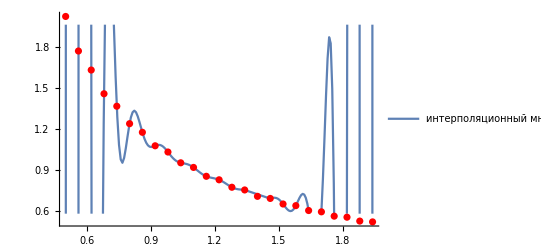

```mathematica
Show[{inplnPlot,pointsPlot}]
```

```mathematica
data12=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,2}];
inpln12:=InterpolatingPolynomial[data12,x];Collect[inpln12,x]
```

10.8129-50.8851 x+137.783 x^2-234.236 x^3+250.95 x^4-148.341 x^5+3.90296 x^6+75.8974 x^7-71.452 x^8+35.4384 x^9-10.4852 x^10+1.7534 x^11-0.128312 x^12

```mathematica
inplnPlot12:=Plot[inpln12,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

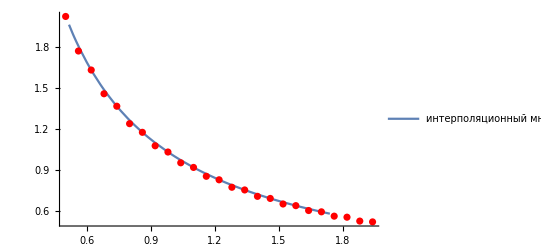

```mathematica
Show[{inplnPlot12,pointsPlot}]
```

```mathematica
data8=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,3}];
```

```mathematica
inpln8:=InterpolatingPolynomial[data8,x];Collect[inpln8,x]
```

135.354-1029.92 x+3392.84 x^2-6229.06 x^3+6962.07 x^4-4854.78 x^5+2065.33 x^6-490.789 x^7+49.9459 x^8

```mathematica
inplnPlot8:=Plot[inpln8,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

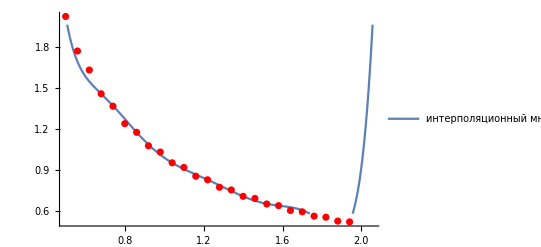

```mathematica
Show[{inplnPlot8,pointsPlot}]
```

```mathematica
data5=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,6}];
```

```mathematica
inpln5:=InterpolatingPolynomial[data5,x];Collect[inpln5,x]
```

5.18212-9.91571 x+8.9416 x^2-3.83138 x^3+0.628092 x^4

```mathematica
inplnPlot5:=Plot[inpln5,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

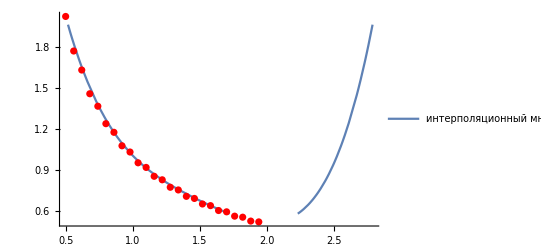

```mathematica
Show[{inplnPlot5,pointsPlot}]
```

```mathematica
spln25:=Interpolation[data25,Method->"Spline"];
```

```mathematica
splnPlot25:=Plot[{spln25[x]},{x,xdata[0]-h,xdata[n]+h},PlotLegends->{"сплайн"},PlotStyle->Green,PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}]
```

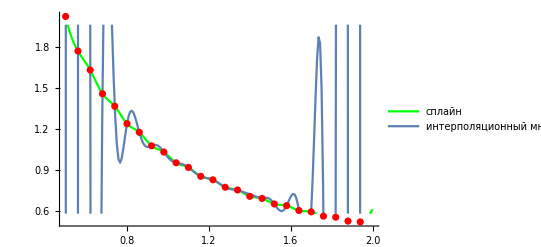

```mathematica
Show[{splnPlot25,inplnPlot,pointsPlot}]
```

```mathematica
spln12:=Interpolation[data12,Method->"Spline"];
```

```mathematica
splnPlot12:=Plot[{spln12[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

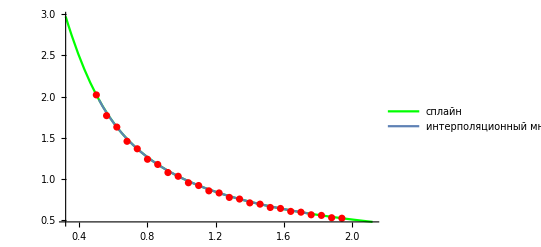

```mathematica
Show[{splnPlot12,inplnPlot12,pointsPlot}]
```

```mathematica
spln8:=Interpolation[data8,Method->"Spline"];
```

```mathematica
splnPlot8:=Plot[{spln8[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

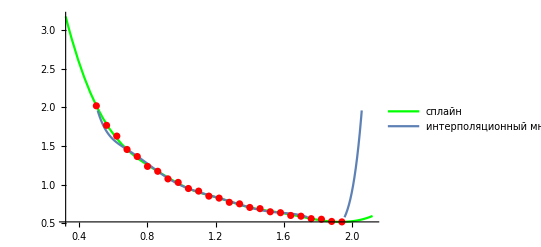

```mathematica
Show[{splnPlot8,inplnPlot8,pointsPlot}]
```

```mathematica
spln5:=Interpolation[data5,Method->"Spline"];
```

```mathematica
splnPlot5:=Plot[{spln5[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

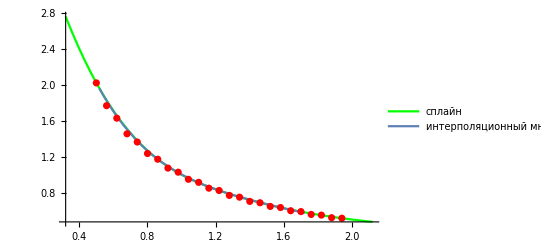

```mathematica
Show[{splnPlot5,inplnPlot5,pointsPlot}]
```

```mathematica
Clear[a,b]
```

```mathematica
rules1=FindFit[data25,a+b*x,{a,b},x];
```

```mathematica
y1=a+b*x/.rules1
f1[x_]:=a+b*x/.rules1;
```

2.03258-0.882873 x

```mathematica
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
```

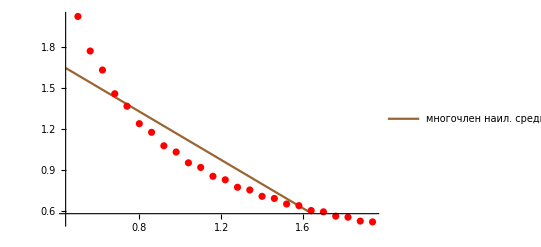

0.532533

```mathematica
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
Clear[a,b]
```

3.09452-2.87422 x+0.816125 x^2

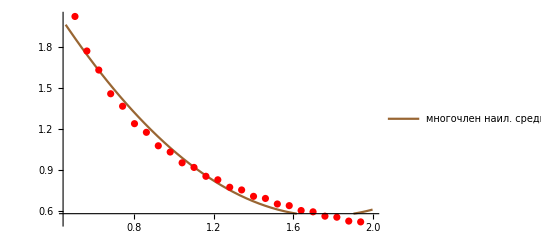

0.0679517

```mathematica
rules1=FindFit[data25,a+b*x+c*x*x,{a,b,c},x];
y1=a+b*x+c*x*x/.rules1
f1[x_]:=a+b*x+c*x*x/.rules1;
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
∑_(i=0)^(n-1) ydata[i]*(xdata[i+1]-xdata[i])
∑_(i=1)^n ydata[i]*(xdata[i]-xdata[i-1])
∑_(i=0)^(n-1) (ydata[i]+ydata[i+1])/2(xdata[i+1]-xdata[i])
h/3*(ydata[0]+ydata[n]+4*∑_(i=1)^(n/2) ydata[2*i-1]+2*∑_(i=1)^(n/2-1) ydata[2*i])
```

1.40197

1.31201

1.35699

1.35135